```mathematica
(* Some sandboxing before the actual algorithm .... *)
```

```mathematica
MemberQ[{1,2,3,4,5},3]
```

True

```mathematica
Block[
{A},
A={5};
Print[A];
A=AppendTo[A,8];
Print[A];
]
```

{5}

{5,8}

```mathematica
Block[
{k},
For[k=1,k≤5,k++,
If[k==4,Continue[],Print[k]];
]
]
```

1

2

3

5

```mathematica
Binomial[6,3]
```

20

```mathematica
AbsoluteTime[]
```

3.831270689951411×10^9

```mathematica
PDF[ProbabilityDistribution[x,{x,1,2}]]
```

Function[x,Piecewise[{{x, 1<x<2}, {0, True}}],Listable]

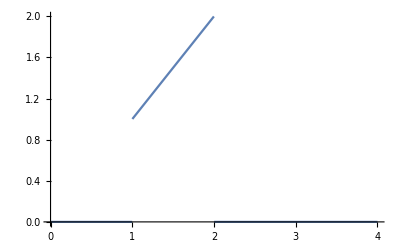

```mathematica
Plot[PDF[ProbabilityDistribution[x,{x,1,2}],x],{x,0,4}]
```

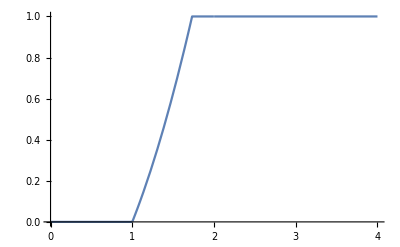

```mathematica
Plot[CDF[ProbabilityDistribution[x,{x,1,2}],x],{x,0,4}]
```

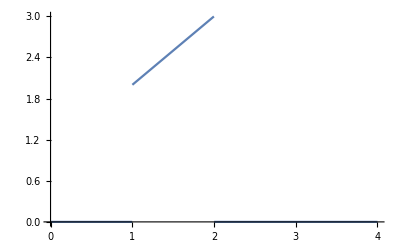

```mathematica
Plot[PDF[ProbabilityDistribution[x+1,{x,1,2}],x],{x,0,4}]
```

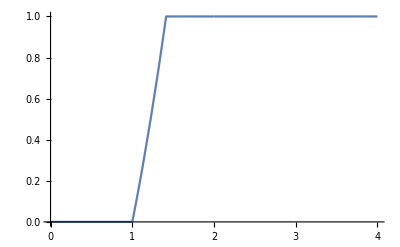

```mathematica
Plot[CDF[ProbabilityDistribution[x+1,{x,1,2}],x],{x,0,4}]
```

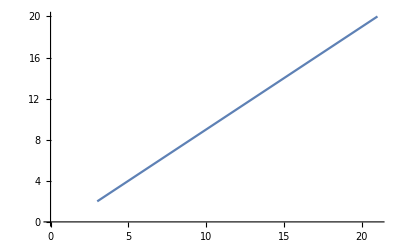

```mathematica
ListLinePlot[Table[PDF[ProbabilityDistribution[x,{x,1,20,1}],x],{x,0,20}]]
```

```mathematica
RandomVariate[NormalDistribution[]]
```

-0.029414

```mathematica
Mean[RandomVariate[ProbabilityDistribution[x,{x,0,20,1}],30]]//N
```

13.1333

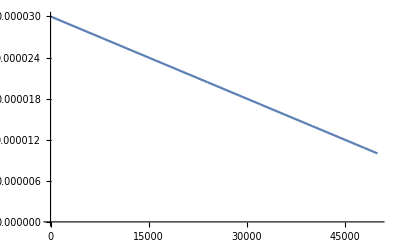

```mathematica
Block[{n=10^5},ListLinePlot[Table[PDF[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}],x],{x,0,n/2}]]]
```

```mathematica
(* The actual algorithm ...*)
```

```mathematica
Block[
{sum,temp,addtemp,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
sum=0;
storebox={};
While[True,
k=RandomInteger[{0,n/2}];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
Print[Log[Abs[sum]]];
]
```

7

23

2.237373631175468930715774×10^9

```mathematica
(* can we try some different distribution ... *)
```

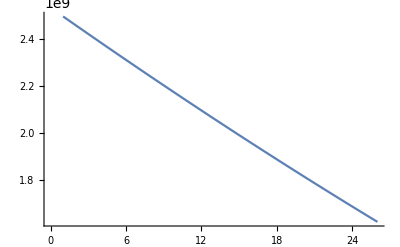

```mathematica
Block[
{k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
ListLinePlot[Table[Log[Abs[Binomial[n/2,k](-1)^k (1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]))]],{k,0,n/2}]]
]
```

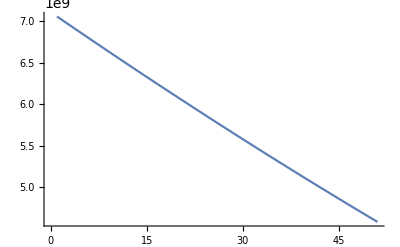

```mathematica
Block[
{k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=100,T=800,P=10^5},
ListLinePlot[Table[Log[Abs[Binomial[n/2,k](-1)^k (1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]))]],{k,0,n/2}]]
]
```

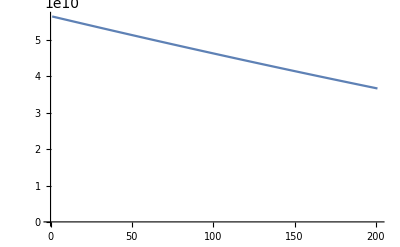

```mathematica
Block[
{k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=400,T=800,P=10^5},
ListLinePlot[Table[Log[Abs[Binomial[n/2,k](-1)^k (1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]))]],{k,0,n/2}],AxesOrigin->{0,0}]
]
```

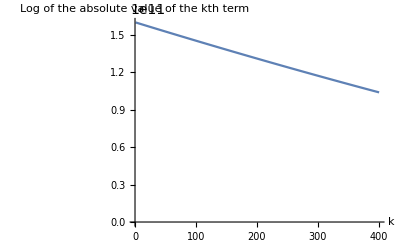

```mathematica
Block[
{k,q=1.6*10^(-19),E0=10^12,kB=1.38*10^(-23),n=800,T=800,P=10^5},
ListLinePlot[Table[Log[Abs[Binomial[n/2,k](-1)^k (1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]))]],{k,0,n/2}],AxesOrigin->{0,0},AxesLabel->{"k","Log of the absolute value of the kth term"}]
]
```

```mathematica
(* I think the uniform distribution works good enough *)
```

```mathematica
Block[
{start,end,sum,temp,addtemp,err=10^(-3),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
sum=0;
storebox={};
While[True,
k=RandomInteger[{0,n/2}];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
start=AbsoluteTime[];
Print[Log[Abs[sum]]];
end=AbsoluteTime[];
Print["Time consumed by Monte Carlo - ",end-start];
start=AbsoluteTime[];
Print[Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}]//Abs//Log];
end=AbsoluteTime[];
Print["Time consumed by total time - ",end-start];
]
```

16

5

1

11

2.457349202969358622730718×10^9

Time consumed by Monte Carlo - 0.00013

2.494675622130928685577666×10^9

Time consumed by total time - 1.84885

```mathematica
Block[
{start,end,sum,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
sum=0;
storebox={};
While[True,
k=RandomInteger[{0,n/2}];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
start=AbsoluteTime[];
Print[Log[Abs[sum]]];
end=AbsoluteTime[];
Print["Time consumed by Monte Carlo - ",end-start];
start=AbsoluteTime[];
Print[Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}]//Abs//Log];
end=AbsoluteTime[];
Print["Time consumed by total time - ",end-start];
]
```

7

1

23

2.457349202969358622730718×10^9

Time consumed by Monte Carlo - 0.0002

2.494675622130928685577666×10^9

Time consumed by total time - 1.88949

```mathematica
(* .... So time consumption is definitely saved by Monte Carlo .... let's do a better job by tweaking the probability distribution a little bit .... *)
```

```mathematica
Block[
{start,end,sum,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=60,T=800,P=10^5,x},
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
start=AbsoluteTime[];
Print[Log[Abs[sum]]];
end=AbsoluteTime[];
Print["Time consumed by Monte Carlo - ",end-start];
start=AbsoluteTime[];
Print[Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}]//Abs//Log];
end=AbsoluteTime[];
Print["Time consumed by total time - ",end-start];
]
```

29

11

24

2.838924457511694719284509×10^9

Time consumed by Monte Carlo - 0.00016

3.279336231101161229140605×10^9

Time consumed by total time - 2.45772

```mathematica
Block[
{start,end,sum,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=100,T=800,P=10^5,x},
sum=0;
storebox={};
start=AbsoluteTime[];
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
Print[Log[Abs[sum]]];
end=AbsoluteTime[];
Print["Time consumed by Monte Carlo - ",end-start];
start=AbsoluteTime[];
Print[Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}]//Abs//Log];
end=AbsoluteTime[];
Print["Time consumed by total time - ",end-start];
]
```

11

16

6.481966439990708017070912×10^9

Time consumed by Monte Carlo - 0.34594

7.056007925152977605579168×10^9

Time consumed by total time - 4.238497

```mathematica
Block[
{start,end,sum,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=200,T=800,P=10^5,x},
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
start=AbsoluteTime[];
Print[Log[Abs[sum]]];
end=AbsoluteTime[];
Print["Time consumed by Monte Carlo - ",end-start];
start=AbsoluteTime[];
Print[Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}]//Abs//Log];
end=AbsoluteTime[];
Print["Time consumed by total time - ",end-start];
]
```

55

9

39

1.9287644473976346594070999×10^10

Time consumed by Monte Carlo - 0.00014

1.9957403651817127532248036×10^10

Time consumed by total time - 12.90812

```mathematica
Block[
{sum,temp,addtemp,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
sum=0;
storebox={};
While[True,
k=RandomInteger[{0,n/2}];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
Print[Log[Abs[sum]]]; (* You got to return this to the function you want to fit it in .... *)
]
```

2.201384147924690004080037×10^9

```mathematica
Block[
{sum,temp,addtemp,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5,x},
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
Print[Log[Abs[sum]]]; (* You got to return this to the function you want to fit it in .... *)
]
```

2.420210827493576229985153×10^9

40 0.13709

40 1.48975

50 0.2349

50 1.87747

60 0.21456

60 2.36793

70 0.16207

70 3.02265

80 0.362846

80 3.848725

90 0.364214

90 4.096401

100 0.18535

100 4.415231

110 0.27955

110 5.277945

120 0.21105

120 7.234025

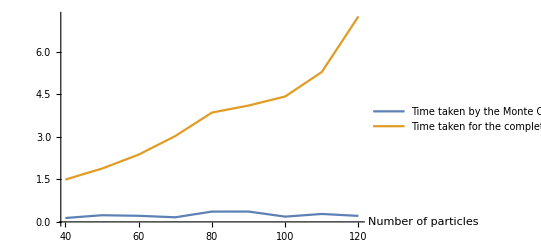

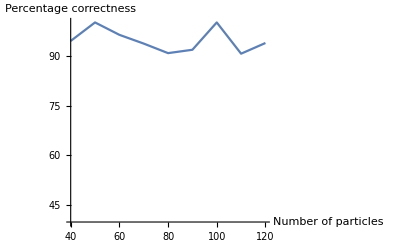

```mathematica
Block[
{start,end,sum,sum1,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n,ActualTime,ExperiTime,sumPercentage,T=800,P=10^5,x},
ActualTime={};
ExperiTime={};
sumPercentage={};
For[n=40,n≤120,n=n+10,
sum=0;
storebox={};
start=AbsoluteTime[];
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
end=AbsoluteTime[];
AppendTo[ExperiTime,{n,end-start}];
Print[n," ",end-start];
start=AbsoluteTime[];
sum1=Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}];
end=AbsoluteTime[];
Print[n," ",end-start];
AppendTo[ActualTime,{n,end-start}];
AppendTo[sumPercentage,{n,Abs[Log[sum]]/Abs[Log[sum1]]*100}];
];
Print[ListLinePlot[{ExperiTime,ActualTime},AxesLabel->{"Number of particles"},PlotLegends->{"Time taken by the Monte Carlo algorithm","Time taken for the complete sum"}]];
Print[ListLinePlot[sumPercentage,AxesLabel->{"Number of particles","Percentage correctness"},AxesOrigin->{40,40}]];
]
```